# Coin toss. Case: w_x0 & w_y0≠0 constant, w_z0=0. Tiberius O. Cheche Faculty of Physics, University of Bucharest June 2016 The code is introduced in COIN TOSS MODELING by RĂZVAN C. STEFAN, TIBERIUS O. CHECHE, ROMANIAN REPORTS IN PHYSICS, Volume 69, Issue3, Article Number 904, Published 2017 http://www.rrp.infim.ro/IP/AN904.pdf

# 1. Euler’s angles transformations

```mathematica
(*Time evolution of Euler angles for the intermediate case for the following type of solutions: *)
alf[t_]:=ao;bet[t_]:=bo+b*t;gam[t_]:=go;

(*Euler rotation matrix, Goldstein p.153*)A[t_]:=FullSimplify[{{Cos[gam[t]]*Cos[alf[t]]-Cos[bet[t]]*Sin[alf[t]]*Sin[gam[t]],Cos[gam[t]]*Sin[alf[t]]+Cos[bet[t]]*Cos[alf[t]]*Sin[gam[t]],Sin[bet[t]]*Sin[gam[t]]},{-Sin[gam[t]]*Cos[alf[t]]-Cos[bet[t]]*Sin[alf[t]]*Cos[gam[t]],-Sin[gam[t]]*Sin[alf[t]]+Cos[bet[t]]*Cos[alf[t]]*Cos[gam[t]],Sin[bet[t]]*Cos[gam[t]]},{Sin[bet[t]]*Sin[alf[t]],-Sin[bet[t]]*Cos[alf[t]],Cos[bet[t]]}},Assumptions:>{go∈Reals,b>0,t>=0,R>0,wx>0,wy>=0,bo>=0,ao>=0}];
```

```mathematica
(* initial vectors at time t=0: *)
ra=A[0].{R,0,0};(* R is coin radius *)
rb=A[0].{0,R,0};

(* normal to initial coin  plane, at t=0: *)
nrarb=FullSimplify[Cross[ra,rb]/Norm[Cross[ra,rb]],Assumptions:>{go∈Reals, b>0,t>=0,R>0,wx>0,wy>=0,bo>=0,ao>=0}];

(*Diaconis theorem:*)
Simplify[nrarb.{wx,wy,0}/.go->-ArcTan[wy/wx]]
```

0

```mathematica
(* rotated vectors: ra->Ara, rb->Arb at time t: *)
Ara[t_]:=A[t].{R,0,0};
Arb[t_]:=A[t].{0,R,0};

(* normal to coin plane at time t: *)
nraprbp[t_]:=FullSimplify[Cross[Ara[t],Arb[t]]/Norm[Cross[Ara[t],Arb[t]]],Assumptions:>{go∈Reals,b>0,t>=0,R>0,wx>0,wy>=0,bo>=0,ao>=0}]
nraprbp[t];
(*Check*)
Simplify[(nraprbp[t]-nrarb)/.t->0]
```

{0,0,0}

```mathematica
(*Diaconis th:*)
Simplify[nraprbp[t].{wx,wy,0}/.go->-ArcTan[wy/wx]]
```

0

```mathematica
(*cosine of dihedral angle as function of time*)
FullSimplify[nrarb.nraprbp[t],Assumptions:>{go∈Reals,b>0,t>=0,R>0,wx>0,wy>=0,bo>=0,ao>=0}]
cos[t_]:=Cos[b t];
```

Cos[b t]

Comments:
Don't set wx=0 because singularity is introduced. This singularity case is solved by this code by taking wy=0 and the desired value of wx; this statement is based on the symmetry of x and y motion.
Initial position of the coin is obtained with ao, bo, go=-ArcTan[wy/wx]. wx, wy are the angular velocities, see section 2.
Dihedral angle between coin planes is only b dependent.

# 2. Parameters of tossing

```mathematica
wx=90;wy=60; (* angular velocities *)
ao=0*Pi/6;bo=0*Pi/6;(*0 value - initially, coin has horizonthal orientation*)
go=-ArcTan[wy/wx]; 
b=√(wx^2+wy^2);
t=0.6;(* time of flight *)
```

# 3. Probability calculus-configurations method (A)

At t=0, S⃗*OverVector[nrarb = ct=]0

At t≠0, S⃗*OverVector[nrarb (t)=ct]=0.

# of rotations = 10.3291

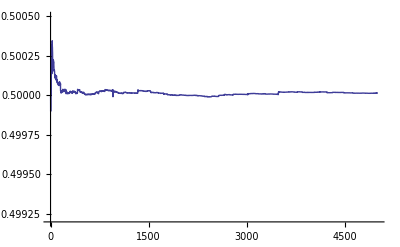

```mathematica
trial=5000; (* number of intervals for the parameters range; the figures in the paper are obtained with trial=5000 with a calculus time about 5 minutes *)

 (* check Diaconis S^(->)*(nrarb=ct)^(->)*)
Print["At t=0, S⃗*OverVector[nrarb = ct=]",Simplify[nrarb.{wx,wy,0}]]
 (* check Diaconis S^(->)*(nrarb=ct)^(->)*)
Print["At t≠0, S⃗*OverVector[nrarb (t)=ct]=",Simplify[nraprbp[t].{wx,wy,0}]]

(*Probability calculus. 5000^2 configurations are considered on the total*)
Clear[L];prob[0]={};i=0;j=0;

Do[bM=b+30*M/trial;
	Do[tL=t+0.3*L/trial;If[cos[bM*tL]>0,i=i+1,j=j+1],
	{L,1,trial}];
prob[M]=Append[prob[M-1],N[i/(i+j)]]
,{M,1,trial}];

Print["# of rotations = ",b*t/(2*Pi)]

(*SetDirectory["C:\Nbook\DiskDAug06\1 Lucrari\Cheche\RRP"];
Export["prob90x60y.dat",prob[trial]];*)
ListPlot[prob[trial],Joined->True,PlotRange->{0.4992,0.5005}]
Clear[trial,i,j];
```

# 4. Probability calculus - method B

# of rotations = 10.3291

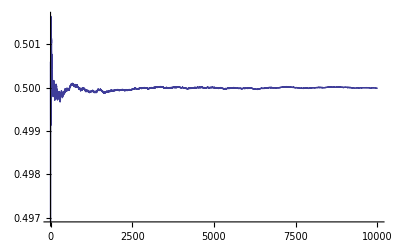

```mathematica
trial=100; (* number of intervals for the parameters range; the figures in the paper are obtained with trial=100 with a calculus time about 15 minutes *)

(*Probability calculus. 100 intervals for the range are used. There are (trial*100)^2 total number of events *)
Clear[L];prob[0]={};i=0;j=0;
Do[bM=b+RandomReal[]*30*M/trial;

Do[tL=t+RandomReal[]*0.3*L/trial;
If[cos[bM*tL]>0,i=i+1,j=j+1],{L,1,100*trial}];
(*Print["H=",i,"; T=",j,"; time=",N[tL],"; Rota=",N[bM*tL/(2*Pi)],"; prob=",N[i/(i+j)]];*)

prob[M]=Append[prob[M-1],N[i/(i+j)]]
,{M,1,100*trial}];

Print["# of rotations = ",b*t/(2*Pi)]

ListPlot[prob[100*trial],Joined->True,PlotRange->All]

(*SetDirectory["C:\Nbook\DiskDAug06\1 Lucrari\Cheche\RRP"];
Export["prob90x60yRandom.dat",prob[100*trial]];*)
Clear[trial,i,j];
```

# 5. Coin orientation

```mathematica
(* Grpaphs for coin planes at t=0 and t *)
p1=ListPlot3D[{{0,0,0},ra/R,rb/R}, PlotStyle->Red,PlotRange->All];
p2=ListPlot3D[{{0,0,0},Simplify[Ara[t]/R],Simplify[Arb[t]/R]}, PlotStyle->Green];

Show[p1,p2, PlotLabel->{"Coin planes: Red t=0; Green t=",t},PlotRange->All,ViewPoint->{Pi,Pi/2,2}](**)

(*http://demonstrations.wolfram.com/ParametricEquationOfACircleIn3D/*)
rc=N[Norm[ra/R]];
nv=nrarb;
 uv=ra/R;
P1[th_]=R*Cos[th]*uv+R*Sin[th]*Cross[nv,uv];
P1p[th_]:=R*Cos[th]*uv+R*Sin[th]*Cross[nv,uv];
Simplify[P1[th]-P1p[th]];

rcp[tt_]:=Norm[Ara[tt]/R];
nvp[tt_]:=nraprbp[tt];
 uvp[tt_]:=Ara[tt]/R;
P2p[th_,tt_]:=R*Cos[th]*uvp[tt]+R*Sin[th]*Cross[nvp[tt],uvp[tt]];
P2[th_]=Simplify[P2p[th,tt]/.tt->t];

Print["# of rotations = ",b*t/(2*Pi)]
```

-Graphics3D-

# of rotations = 10.3291

```mathematica
(* Drawing oriented coins: *)
(*http://mathematica.stackexchange.com/questions/10811/how-do-i-fill-in-a-circle-made-by-parametricplot-with-one-solid-color*)
pp1=ParametricPlot3D[v*P1[th]/R,{th,0,2*Pi},{v,0,1},Mesh->{0,{1}},MeshStyle->Thick,PlotStyle->Opacity[0.5,Red]];

pp2=ParametricPlot3D[(v*P2[th]/R),{th,0,2*Pi},{v,0,1},Mesh->{0,{1}},MeshStyle->Thick,PlotStyle->Opacity[0.5,Blue]];

Show[pp2,pp1, PlotRange->{{-1,1},{-1,1},{-1,1}},AxesLabel->{Style[Subscript[x, 1],Large,Bold,Red],Style[Subscript[y, 1],Large,Bold,Blue],Style[Subscript[z, 1],Large,Bold,Blue]},LabelStyle->Directive[White],BoxStyle->Directive[Dashed],ViewPoint->{Pi,Pi/2,2}]
```

-Graphics3D-

```mathematica
pts={{0,0,0},nraprbp[t]};
pts1={{0,0,0},{wx,wy,0}};
Show[pp2,pp1,ListPointPlot3D@pts,Graphics3D@Line@pts,ListPointPlot3D@pts1,Graphics3D@Line@pts1,AxesLabel->{Style[Subscript[x, 1],Large,Bold,Red],Style[Subscript[y, 1],Large,Bold,Blue],Style[Subscript[z, 1],Large,Bold,Blue]},LabelStyle->Directive[White],PlotRange->{{-1,1},{-1,1},{-1,1}}]
```

-Graphics3D-

```mathematica
Clear[ao,bo,wx,wy,go,b,t,i,j];
```